```mathematica
Exit[]
```

Metric Coefficients:

```mathematica
gtt[r_,a_,theta_]:=-1+2*M/r 
gtphi[r_,a_,theta_]:=0 
gphiphi[r_,a_,theta_]:=r^2*Sin[theta]^2
```

Mass of the Black Hole

```mathematica
M:=1
```

Marginally Bound Orbit Radius

```mathematica
rmb:=4*M
```

Marginally Stable Orbit Radius

```mathematica
rms:=6*M
```

Keplerian Angular Velocity

```mathematica
OmegaK[r_,a_,theta_]:=M^(1/2)/(r^(3/2)+a*M^(1/2))
```

Keplerian Angular Momentum

```mathematica
lK[r_,a_,theta_]:=-(gtphi[r,a,theta]+OmegaK[r,a,theta]*gphiphi[r,a,theta])/(gtt[r,a,theta]+OmegaK[r,a,theta]*gtphi[r,a,theta])
```

Keplerian Angular Momentum of the MB orbit

```mathematica
lmb:=lK[rmb,0,π/2]
```

```mathematica
lmb
```

4

Keplerian Angular Momentum of the MS orbit

```mathematica
lms:=lK[rms,0,π/2]
```

```mathematica
lms
```

3 √(3/2)

Angular Momentum of the Torus in terms of the adimensional parameter Lambda

```mathematica
l[lambda_]:=lambda*(lmb-lms)+lms
```

Angular Velocity of the Torus

```mathematica
Omega[r_,a_,theta_,lambda_]:=-(gtphi[r,a,theta]+l[lambda]*gtt[r,a,theta])/(gphiphi[r,a,theta]+l[lambda]*gtphi[r,a,theta])
```

Potential Function W

```mathematica
W[r_,a_,theta_,lambda_]:=1/2 Log[-(gtt[r,a,theta]+2*gtphi[r,a,theta]*Omega[r,a,theta,lambda]+gphiphi[r,a,theta]*(Omega[r,a,theta,lambda])^2)/(gtt[r,a,theta]+Omega[r,a,theta,lambda]*gtphi[r,a,theta])^2]
```

Potential Function W modified

```mathematica
W1[r_,a_,theta_,lambda_]:=-(gtt[r,a,theta]+2*gtphi[r,a,theta]*Omega[r,a,theta,lambda]+gphiphi[r,a,theta]*(Omega[r,a,theta,lambda])^2)/(gtt[r,a,theta]+Omega[r,a,theta,lambda]*gtphi[r,a,theta])^2
```

Contour Plot of W modified in Cartesian Coordinates (x,z)

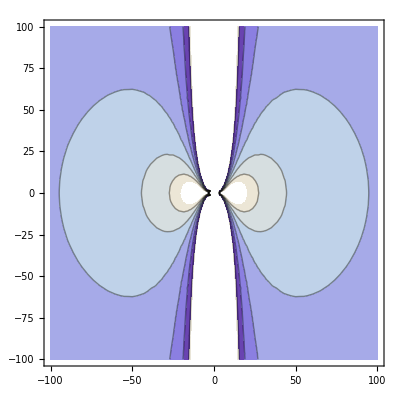

```mathematica
ContourPlot[W1[Sqrt[x^2+z^2],0,ArcSin[x/Sqrt[x^2+z^2]],0.3],{x,-100,100},{z,-100,100}]
```

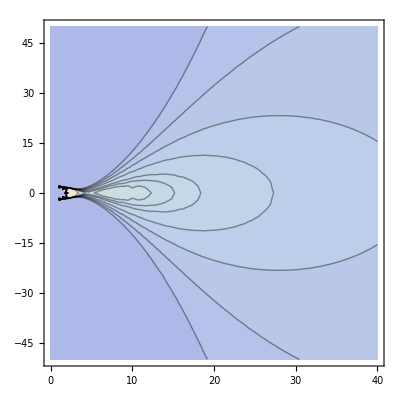

```mathematica
ContourPlot[{W1[Sqrt[x^2+z^2],0,ArcSin[x/Sqrt[x^2+z^2]],0.3]},{x,0,40},{z,-50,50},Contours->{1.2,1.1,1.09,1.08,1.06,1.04,1.02,1.0,0,-0.2,-1},ClippingStyle->Automatic]
```

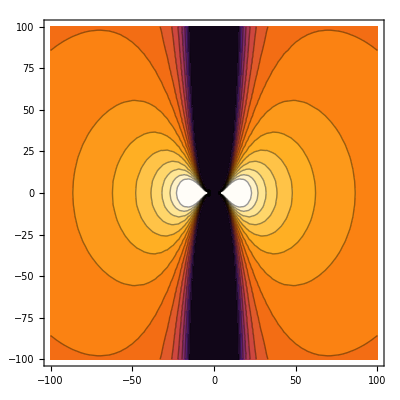

```mathematica
ContourPlot[W1[Sqrt[x^2+z^2],0,ArcSin[x/Sqrt[x^2+z^2]],0.3],{x,-100,100},{z,-100,100},Contours->20,ClippingStyle->Automatic, ColorFunction->{"SunsetColors"}]
```